## Load Data

```mathematica
{{ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
Keys[mydata]

dαs=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
αs=mydata["Alpha"];
urs=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
uτs=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
rs=mydata["Radius"];(*in IGeV*)
Drs=mydata["RadialDerivative"];(*in IGeV*)
τs=mydata["Time"];(*in IGeV*)
Dτs=mydata["TimeDerivative"];(*in IGeV*)}, {□}}
```

{{{BackgroundFields Null^10,Alpha Null^10,Time Null^10,Radius Null^10,NumberOfPoints Null^10,TimeDerivative Null^10,RadialDerivative Null^10,MidpointRule Null^10,rStart Null^10,tStart Null^10,CentralityClass Null^10}},{□}}

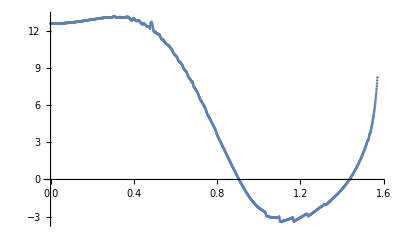

```mathematica
ListPlot[Transpose@{αs,Drs}]
```

The αs are not at all evenly spaced and their spacing varies quite discontinuously.

### Define Interpolating Functions from the Data

NOTATION: an object named "fs" (where "f" stands for any of τ,α,ur,...) refers to an array of values of the corresponding quantity evaluated on the freezeout surface, as a function of α. So Transpose{αs,fs} are the (x,y)-value pairs corresponding to the function f[α]. Here we reconstruct the corresponding functions from interpolation, assuming they are sufficiently smooth and well resolved. The necessity of interpolated functions on the FO surface becomes clear later on.

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

Maybe Fitting is even better, curves will be smoother. If the data has discontinuities, so does the interpolating curve. Unlike the fitting curve.

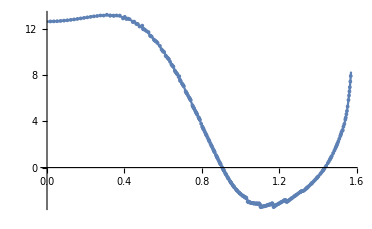

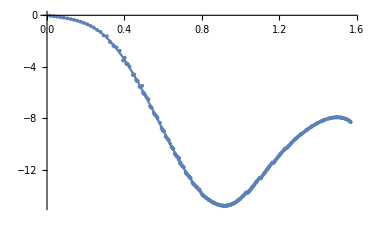

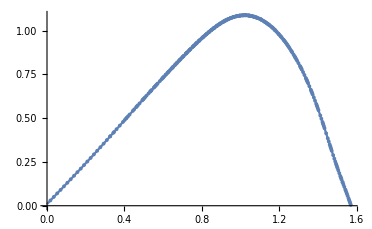

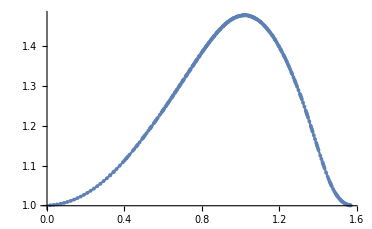

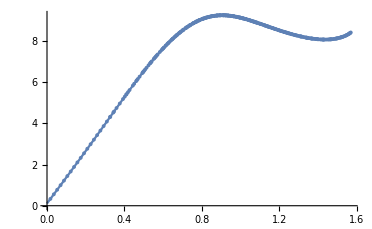

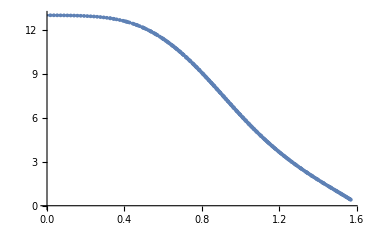

```mathematica
ndegree=55;(*14,25,43,44,55*)
monomials=Table[x^i,{i,0,ndegree}];
ur[α_]=Fit[Transpose@{αs,urs},monomials,x]/.x->α;
uτ[α_]=Fit[Transpose@{αs,uτs},monomials,x]/.x->α;
r[α_]=Fit[Transpose@{αs,rs},monomials,x]/.x->α;
Dr[α_]=Fit[Transpose@{αs,Drs},monomials,x]/.x->α;
τ[α_]=Fit[Transpose@{αs,τs},monomials,x]/.x->α;
Dτ[α_]=Fit[Transpose@{αs,Dτs},monomials,x]/.x->α;
Show[
Plot[Dr[x],{x,0,Pi/2}],
ListPlot[Transpose@{αs,Drs}]
]
Show[
Plot[Dτ[x],{x,0,Pi/2}],
ListPlot[Transpose@{αs,Dτs}]
]
Show[
Plot[ur[x],{x,0,Pi/2}],
ListPlot[Transpose@{αs,urs}]
]
Show[
Plot[uτ[x],{x,0,Pi/2}],
ListPlot[Transpose@{αs,uτs}]
]
Show[
Plot[r[x],{x,0,Pi/2}],
ListPlot[Transpose@{αs,rs}]
]
Show[
Plot[τ[x],{x,0,Pi/2}],
ListPlot[Transpose@{αs,τs}]
]
```

## Compute Field on Freezeout Surface

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
mσ=0.6;(*mass of the sigma field ~ 400-800 MeV*)
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ϵ=0.001*0.160054;(*energy density at freeze out in GeV/(fm^3)*)
vev=0.09;(*??? vev of sigma field ??? pion decay constant ~92MeV ???, in GeV*)
```

```mathematica
Quiet[
{
(*Why does this not work with "=" instead of ":="*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
     linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];

Nαs=1500;
αs=linspace[0,Pi/2,Nαs];
dαs=(Pi/2)/Nαs;
urs=ur[αs]; (*dimensionless*)
uτs=uτ[αs]; (*dimensionless*)
rs=r[αs];(*in IGeV*)
Drs=Dr[αs];(*in IGeV*)
τs=τ[αs];(*in IGeV*)
Dτs=Dτ[αs];
},
{InterpolatingFunction::dmval}];
```

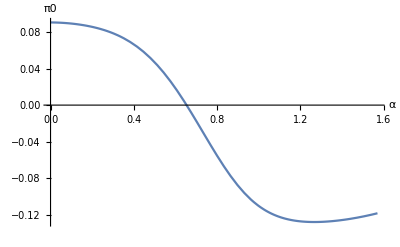

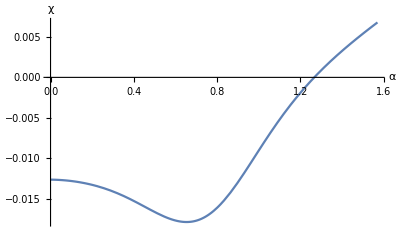

```mathematica
ratio=0.5;
sign=-1;
Epot = ratio*ϵ;
Ekin=(1-ratio)*ϵ;
π0start=Sqrt[2*Epot]/mπ;
χstart=sign*Sqrt[2*Ekin];

ODEs={
π0'[α]==χ[α]*(-Dτ[α]*uτ[α]+Dr[α]*ur[α]),
χ'[α]==-mπ^2*π0[α]*(-Dτ[α]*uτ[α]+Dr[α]*ur[α])};
ICs={π0[0]==π0start,χ[0]==χstart};
solution=NDSolve[{ODEs,ICs},{π0[α],χ[α]},{α,0,Pi/2}];
π0func[t_]:=(π0[α]/.solution[[1]]/.α->t);
χfunc[t_]:=(χ[α]/.solution[[1]]/.α->t);

Plot[π0func[x],{x,0,Pi/2},AxesLabel->{α,π0}]
Plot[χfunc[o],{o,0,Pi/2},AxesLabel->{α,χ}]
```

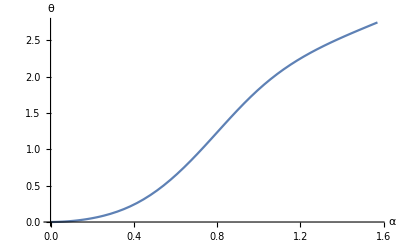

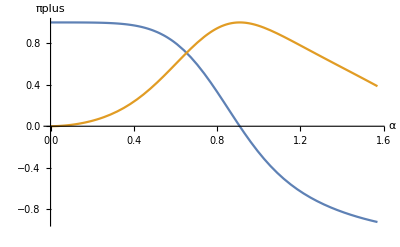

```mathematica
χθ=mπ;
n=1;

ODEs={θ'[α]==χθ*(-Dτ[α]*uτ[α]+Dr[α]*ur[α])};
ICs={θ[0]==0};
solution=NDSolve[{ODEs,ICs},{θ[α]},{α,0,Pi/2}];
θfunc[t_]:=(θ[α]/.solution[[1]]/.α->t);
πplus[t_]:=Sqrt[n]*Exp[I*θfunc[t]]

Plot[θfunc[x],{x,0,Pi/2},AxesLabel->{α,θ}]
Plot[{Re@πplus[x],Im@πplus[x]},{x,0,Pi/2},AxesLabel->{α,πplus}]
```

## Compute the Fourier Spectrum of the Source

First, define a set of helper functions. These depend on the (transverse) momentum p_ and the coordinate α_ on the Freezeout surface. Eventually we wish to integrate over the Freezeout surface. The dependence on p_ can be substituted by explicit evaluation on a (nicely resolved) grid in momentum space. The dependence on α_ must remain symbolic, since we wish to numerically integrate over α_ using NIntegrate.

```mathematica
ω[p_]=Sqrt[p^2+mπ^2];(*in GeV (p in GeV) *)
J0rp[α_,p_]=BesselJ[0,r[α]*p*GeVtoIfm];(*dimensionless*)
J1rp[α_,p_]=BesselJ[1,r[α]*p*GeVtoIfm];(*dimensionless*)
Y0tw[α_,p_]=BesselY[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[α_,p_]=BesselY[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[α_,p_]=BesselJ[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[α_,p_]=BesselJ[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)

G0[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p]);(*dimensionless*)
G0ANTI[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p]);(*dimensionless*)
G1[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]+I*J1tw[α,p]);(*dimensionless*)
G1ANTI[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]-I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*ω[p]*J0rp[α,p]*(-Y1tw[α,p]-I*J1tw[α,p]);(*dimensionless*)
```

NOTATION: an object named "fps" with f some quantity represents a function f[p_,...] with the p_-dependence evaluated explicitly on the momentum grid given by "ps".

The most ressource heavy computation happens here, due to the use of NIntegrate. The routine (probably) uses more and more subdivisions for the large-p_ components in H(1/2)ps.

WHY USE NINTEGRATE AND INTERPOLATED FUNCTIONS? Discrete Fourier Transform, say  on  an  Interval [0, L], discretized  with  N  points, shows  and  alias  effect  and  is  valid  only  up  to  the  Nyquist  frequency  (~ momentum)  (2?)  Nπ/L  and  the  spectrum  will  then  continue  periodically  (just  as  the  real  space  function  will, if  calculated  from  discretized  momentum  grid . There  will  thus  be  no  convergence  to  0  for  large  momenta . It  is  not  immediately  clear  to  me  how  this  effect  is  altered  when  using  Bessel  functions  and  the  integral  measure  in  polar  coordinates, but  qualitatively  this  should  prevent  convergence  to  0  of  the  spectrum  for  large  p, which  would  be  necessary  for  a  physical  spectrum . 
    
    One  could  simply  apply  a  finer  discretization  in  real  space  (= finer  mesh  of  αs), but  I  expect  the  effect  to  be  worse  for  larger  momenta . The  routine  NIntegrate  automatically  chooses  and  refines  the  grid  of  αs  in  real  space, until  the  integral  has  converged  sufficiently  well . For  low  p_  it  is  expected  that  the  grid  specified  by  the  raw  data  is  enough . For  large  p_  a  finer  grid  should  be  chosen . We  should  thus  provide  (interpolated)  functions  of  α_  such  that  this  refinement  through  the  integration  routine is dynamically possible .

```mathematica
ComputeSourceSpectr[ps_,f_,Df_]:=Module[{H1ps,H2ps,spectrps},
(*
f is supposed to be the π-field, Df it's perpendicular derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]

The name π is protected!!!
*)
G0ps[α_]=G0[α,ps];
G1ps[α_]=G1[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0ps[α]+f[α]*G1ps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
ComputeSourceSpectrAnti[ps_,f_,Df_]:=Module[{H1ps,H2ps,spectrps},
(*
f is supposed to be the π-field, Df it's perpendicular derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]

The name π is protected!!!
*)
G0ANTIps[α_]=G0ANTI[α,ps];
G1ANTIps[α_]=G1ANTI[α,ps];

spectrps=2*Pi^2*NIntegrate[
τ[α]*r[α]*fmtoIGeV^2*(Df[α]*G0ANTIps[α]+f[α]*G1ANTIps[α]),{α,0,Pi/2},
Method->{Automatic,"SymbolicProcessing"->0}
];
spectrps
]
```

```mathematica
ps=linspace[0,1,100];
myf[x_]=π0func[x];
myDf[x_]=χfunc[x]*(-Dr[x]*uτ[x]+Dτ[x]*ur[x]);
Jπspec=ComputeSourceSpectr[ps,myf,myDf];
JπspecAnti=ComputeSourceSpectrAnti[ps,myf,myDf];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -114.689+153.095 ⅈ and 0.00249523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -114.48+145.992 ⅈ and 0.00240156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -113.008+125.819 ⅈ and 0.00212094 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -114.689-153.095 ⅈ and 0.00249523 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -114.48-145.992 ⅈ and 0.00240156 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -113.008-125.819 ⅈ and 0.00212094 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
ps=linspace[0,1,100];
myf[x_]=πplus[x];
myDf[x_]=I*πplus[x]*mπ*(-Dr[x]*uτ[x]+Dτ[x]*ur[x]);
Jπspec=ComputeSourceSpectr[ps,myf,myDf];
JπspecAnti=ComputeSourceSpectrAnti[ps,myf,myDf];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -517.813+3069.89 ⅈ and 0.0412418 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -586.598+2949.74 ⅈ and 0.0396674 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -763.069+2599.88 ⅈ and 0.0359291 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 106.566-942.832 ⅈ and 0.0358512 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 67.3406-935.332 ⅈ and 0.0345682 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -42.9927-904.845 ⅈ and 0.0314847 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

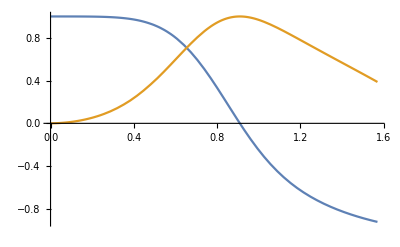

```mathematica
Plot[{Re@myf[x],Im@myf[x]},{x,0,Pi/2}]
```

InterpolatingFunction::dmval: Input value {0.0000320891} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

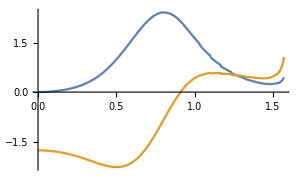

```mathematica
Plot[{Re@myDf[x],Im@myDf[x]},{x,0,Pi/2}]
```

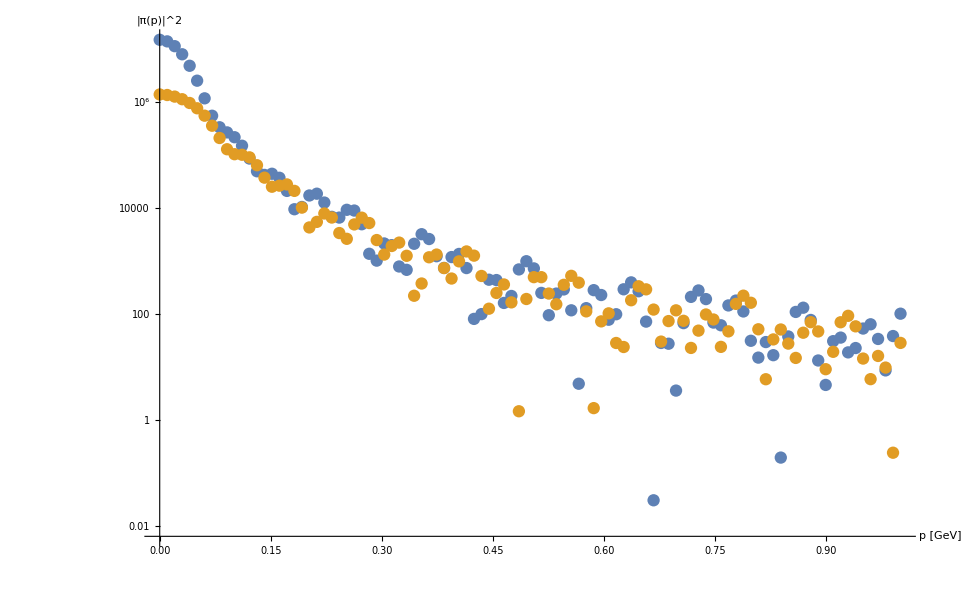

```mathematica
ListLogPlot[
{
Transpose@{ps,(1/(2*Pi)^3)*Abs[Jπspec]^2},
Transpose@{ps,(1/(2*Pi)^3)*Abs[JπspecAnti]^2}},
AxesLabel->{"p [GeV]","|π(p)|^2"}]
```

```mathematica
ps=linspace[0,2,200];
myf[x_]=Sin[11.4*x]*Exp[-(x-1.4*I)^2];
myDf[x_]=Cos[12-7*x]*Exp[-3*(x-0.7*I)^2];
Jπspec=ComputeSourceSpectr[ps,myf,myDf];
JπspecAnti=ComputeSourceSpectrAnti[ps,myf,myDf];
```

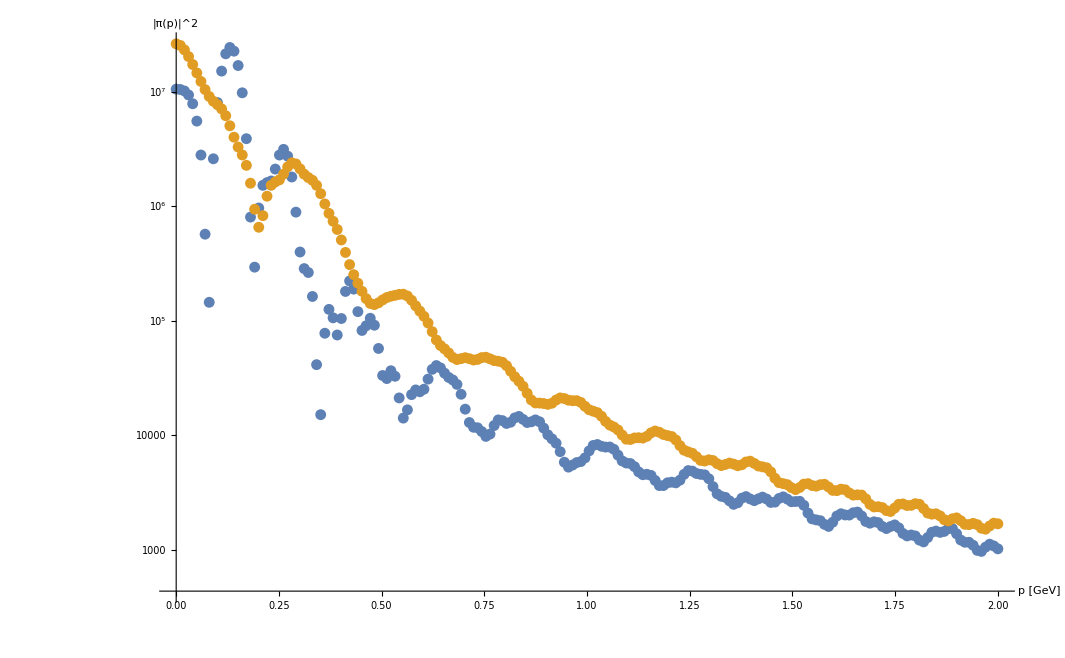

```mathematica
ListLogPlot[
{
Transpose@{ps,(1/(2*Pi)^3)*Abs[Jπspec]^2},
Transpose@{ps,(1/(2*Pi)^3)*Abs[JπspecAnti]^2}},
AxesLabel->{"p [GeV]","|π(p)|^2"}]
```

```mathematica
ps=linspace[0,10,50];
myf[x_]=1;
myDf[x_]=0;
Jπspec=ComputeSourceSpectr[ps,myf,myDf];
JπspecAnti=ComputeSourceSpectrAnti[ps,myf,myDf];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.5522862897358791663127153270806957152672111988067626953125}. NIntegrate obtained -0.148433-1.63473 ⅈ and 3.89962×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.45726}. NIntegrate obtained -0.287547-1.29328 ⅈ and 3.27472×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.534751694686307850468143243460872326977550983428955078125}. NIntegrate obtained -2.70115-0.993333 ⅈ and 4.87419×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.5522862897358791663127153270806957152672111988067626953125}. NIntegrate obtained -0.148433+1.63473 ⅈ and 3.89962×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.45726}. NIntegrate obtained -0.287547+1.29328 ⅈ and 3.27472×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.534751694686307850468143243460872326977550983428955078125}. NIntegrate obtained -2.70115+0.993333 ⅈ and 4.87419×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

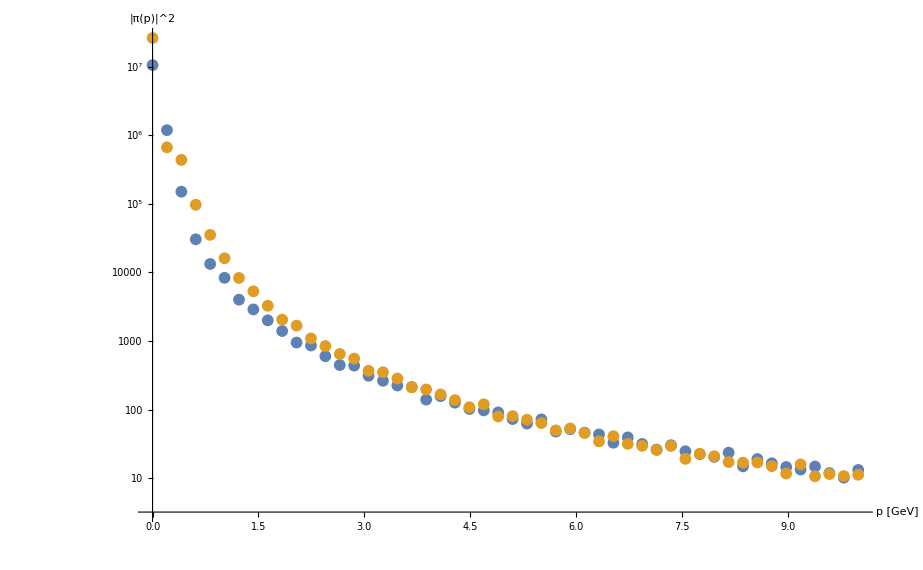

```mathematica
ListLogPlot[
{
Transpose@{ps,(1/(2*Pi)^3)*Abs[Jπspec]^2},
Transpose@{ps,(1/(2*Pi)^3)*Abs[JπspecAnti]^2}},
AxesLabel->{"p [GeV]","|π(p)|^2"}]
```

## Compare to Alice Data

```mathematica
Alicedatatxt=Import[StringJoin[NotebookDirectory[],"data/HEPData-ins1222333-v1-Table_1.csv"],"Text"];
(*Alicedata=ImportString[StringReplace[StringReplace[Alicedatatxt,RegularExpression["\n+"]->"\n"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV"];*)
Alicedata=ImportString[StringReplace[Alicedatatxt,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV","IgnoreEmptyLines"->True];
MatrixForm[Alicedata];
titles=Alicedata[[1]];
enumeratedtitles=Transpose[{Range[Length[titles]],titles}]
πplusALICE=Alicedata[[2;;42]];
πminusALICE=Alicedata[[44;;]];
aliceps=(Transpose@πplusALICE)[[1]];
aliceyieldplus=(Transpose@πplusALICE)[[4]];
aliceyieldminus=(Transpose@πminusALICE)[[4]];
```

{{1,PT [GEV]},{2,PT [GEV] LOW},{3,PT [GEV] HIGH},{4,(1/Nev)*(1/(2*PI*PT))*D2(N)/DPT/DYRAP [GEV**-2]},{5,stat +},{6,stat -},{7,sys +},{8,sys -},{9,sys,normalization uncertainty +},{10,sys,normalization uncertainty -}}

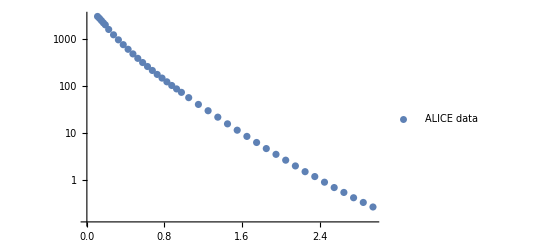

```mathematica
ListALICE=Transpose@{aliceps,aliceyieldplus+aliceyieldminus};
ListLogPlot[
ListALICE,
PlotLegends->{"ALICE data"}
]
```

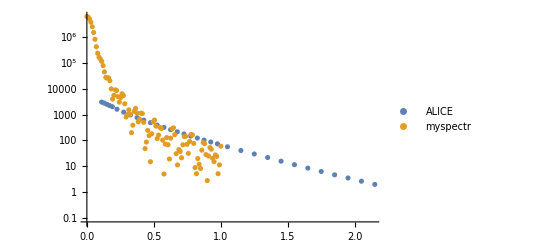

```mathematica
Quiet[
ListLogPlot[
{ListALICE,Transpose@{ps,1/(2*Pi)^3*Abs[Jπspec]^2}},
PlotLegends->{"ALICE","myspectr"}
]
,{Transpose::nmtx}]
```